```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
$PrePrint=StandardForm;
```

```mathematica
(* Load helper functions *)
<<CrossSection`
(* Load Kiselev's cross sections (corrected for PV state) *)
<<TreeLevelKnownCrossSections`

nb = 0.3894 10^6;
pb =10^3 nb;
fb =10^6 nb;
μb =10^-3 nb;
(*mb =10^-6 nb;*)
AllStates = {"PP","PV", "VV"};
zAllStates = {"zPP","zPV", "zVV"};
AllStatesWithZ = Join[AllStates,zAllStates];
 (*Load data *)
ReadData["amps_"<>#,#]&/@AllStates;
ReadData["z_amps_"<>#,"z"<>#]&/@AllStates;
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
(* Check that analytical tree level cross section for gamma is equal to Kiselev *)
FullSimplify[ (DsDCosThetaTreeAnalytic[#]/.gStrong->√(4π alphaS))/$Kiselev[#]]&/@AllStates
```

{1,1,1}

```mathematica
(* Check that divergent counterterms are cancelled for gamma and PP, PV for Z*)
Factor[( LoadedAmplitudes[#]["treeCounterterms"]+LoadedAmplitudes[#]["loopCounterterms"])&/@(AllStates~Join~{"zPP","zPV"})]
```

{0,0,0,0,0}

```mathematica
(* Check whether Hypergeometric2F1 present in finit part (eps-terms) *)
FreeQ[LoadedAmplitudes[#]["loop"],Hypergeometric2F1]&/@AllStatesWithZ
```

{False,False,False,False,False,False}

```mathematica
(* Check that numerical tree level for gamma equals exactly to Kiselev result *)
Module[{s=1000,μ=$MC+$MB,cos = 0.112312, expected, actual},
(actual = DsDCosTheta[#,s,cos][[1]];
expected = NN@$Kiselev[#,s,cos];
Chop[expected-actual[[1]],10^-8])&/@AllStates
]
```

{0,0,0}

```mathematica
(* Calculate tree level cross sections analytic (both gamma + Z)*)
(*Print[Dynamic[state]];
Do[
DsDCosThetaTree[state]=DsDCosThetaTreeAnalytic[state];,
{state,AllStatesWithZ}];
Export[#<>"DsDCosThetaTree.m",DsDCosThetaTree[#]]&/@AllStatesWithZ;*)
```

```mathematica
(* Calculate tree level cross sections analytic (both gamma + Z)*)
(*Print[Dynamic[state]];
Do[
CrossSectionTree[state]=CosIntegrate[DsDCosThetaTree[state]]//Factor;,
{state,AllStatesWithZ}];Export[#<>"CrossSectionTree.m",CrossSectionTree[#]]&/@AllStatesWithZ;*).10.10
```

```mathematica
(* Integrating to obtain full cross sections *)
PrintTemporary[Dynamic[state]];
Do[
FullCrossSections[state]=({#⟦1⟧,Integrate[#⟦2⟧,{cos,-1,1}]})&/@DsDCosThetaCache[state];,
{state,AllStates}];
```

```mathematica
(* Check again that tree level match Kiselev's results *)
Do[
Block[{ki, fBc=0.5, alphaS=0.3},
ki = NN@$Kiselev[state];
ki = Integrate[ki,{cos,-1,1}];
Print[((ki/.s->(#⟦1⟧)^2)/#⟦2,1⟧)&/@FullCrossSections[state]];
],
{state,AllStates}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Do[
Block[{alphaS = 0.3, fBc = 1,temp, ecm,cs,str = "",pr},
pr[x_]:=NumberForm[x,5];
ecm =FullCrossSections["PP"][[nn]][[1]];
str = str <>"при sqrt(s) = " <> ToString[ecm] <> " GeV, ";
Do[
 temp = FullCrossSections[st][[nn]];
cs = fb temp[[2]];
str = str<>"sigma("<>st<>") = " <>ToString@pr[cs[[1]]] <>" fb " <> Module[{s =  ToString@pr[cs[[2]]]},If[ StringStartsQ[s,"-"],s,"+"<>s]]<>" fb, ";
,{st, AllStates}];
Print@str;
],{nn,{10,25,35}}]
```

при sqrt(s) = 15.1047 GeV, sigma(PP) = 2.7174 fb -1.7756 fb, sigma(PV) = 50.589 fb +57.963 fb, sigma(VV) = 206.5 fb +144.77 fb,

при sqrt(s) = 22.6047 GeV, sigma(PP) = 1.8104 fb -0.11538 fb, sigma(PV) = 3.8319 fb +4.7593 fb, sigma(VV) = 16.53 fb +9.4833 fb,

при sqrt(s) = 27.6047 GeV, sigma(PP) = 0.79865 fb -0.055834 fb, sigma(PV) = 0.88509 fb +1.1525 fb, sigma(VV) = 4.1545 fb +1.9737 fb,

```mathematica
Do[
Block[{alphaS = 0.3, fBc = 1,temp, ecm,cs,str = "",pr},
pr[x_]:=NumberForm[x,5];
ecm =FullCrossSections["PP"][[nn]][[1]];
str = str <>"при sqrt(s) = " <> ToString[ecm] <> " GeV, ";
Do[
 temp = FullCrossSections[st][[nn]];
cs = fb temp[[2]];
str = str<>"sigma("<>st<>") = " <>ToString@pr[cs[[1]]] <>" fb " <> Module[{s =  ToString@pr[cs[[2]]]},If[ StringStartsQ[s,"-"],s,"+"<>s]]<>" fb, ";
,{st, AllStates}];
Print@str;
],{nn,{10,25,35}}]
```

при sqrt(s) = 15.1047 GeV, sigma(PP) = 2.6797 fb -1.7509 fb, sigma(PV) = 49.888 fb +57.159 fb, sigma(VV) = 203.64 fb +142.77 fb,

при sqrt(s) = 22.6047 GeV, sigma(PP) = 1.7853 fb -0.11378 fb, sigma(PV) = 3.7787 fb +4.6933 fb, sigma(VV) = 16.3 fb +9.3518 fb,

при sqrt(s) = 27.6047 GeV, sigma(PP) = 0.78758 fb -0.05506 fb, sigma(PV) = 0.87282 fb +1.1365 fb, sigma(VV) = 4.0969 fb +1.9463 fb,

```mathematica
Block[{alphaS = 0.3, fBc = 1,temp},
Do[
 temp = FullCrossSections[st][[35]];
Print[{temp[[1]],fb temp[[2;;]]}];
,{st, AllStates}];
]
```

{27.6047,(0.787575 | -0.0550598)}

{27.6047,(0.872818 | 1.13652)}

{27.6047,(4.09686 | 1.94629)}

```mathematica
mus=Table[i,{i,$MC+$MB,10000,500}];
Block[{alphaS=0.25,fBc=0.5},
muDep = FullCrossSection["PP",900,#]&/@mus;
];
```

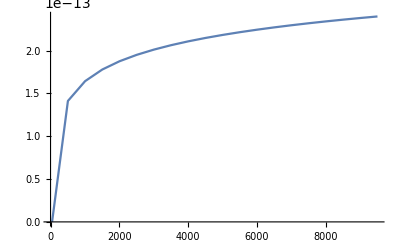

```mathematica
ListPlot[Transpose@{mus,(Total@#)&/@muDep},Joined->True]
```

```mathematica
CosThetaPlots={};
Do[
Block[{ecm,fBc=0.5,alphaS=0.25,tree,loop,total,plot},
ecm = DsDCosThetaCache[state]⟦10,1⟧;
Print["E.c.m. = " <> ToString[ecm]];
tree=fb DsDCosThetaCache[state]⟦10,2,1⟧;
loop=fb DsDCosThetaCache[state]⟦10,2,2⟧;
total = tree+loop;
plot = Plot[{tree,loop,total},{cos,-1,1},
Frame->True,FrameLabel->{{"dσ/dcosθ, fb",""},{"cosθ",""}},
PlotStyle->{Directive[Red,Dashed],Directive[Blue,DotDashed],Black}
,PlotLegends->{state<>" LO",state<>" 1loop",state<>" total"}
];
AppendTo[CosThetaPlots,plot];
],
{state,AllStates}]
```

E.c.m. = 15.1047

E.c.m. = 15.1047

E.c.m. = 15.1047

```mathematica
GraphicsGrid[{CosThetaPlots},ImageSize->1000]
```

-Graphics-

```mathematica
FullCrossSectionPlots={};
Do[
Block[{fBc=0.5,alphaS=0.25,x,tree,loop,total,kfactor,plot},
x=FullCrossSections[state]⟦All,1⟧;
tree=Transpose@{x,fb FullCrossSections[state]⟦All,2,1⟧};
loop =Transpose@{x,fb FullCrossSections[state]⟦All,2,2⟧};
total =Transpose@{x,tree⟦All,2⟧+loop⟦All,2⟧};
kfactor = Transpose@{x,total⟦All,2⟧/tree⟦All,2⟧};
plot=ListPlot[
{tree,loop,total},
Joined->True,
PlotRange->All,
Frame->True,FrameLabel->{{"σ, fb",""},{"√s, GeV",""}},
PlotStyle->{Directive[Red,Dashed],Directive[Blue,DotDashed],Black},
PlotLegends->{state<>" LO",state<>" 1loop",state<>" total"}
];
AppendTo[FullCrossSectionPlots,plot];
KFactors[state]=kfactor;
],
{state,AllStates}];
```

```mathematica
GraphicsGrid[{FullCrossSectionPlots},ImageSize->1000]
```

-Graphics-

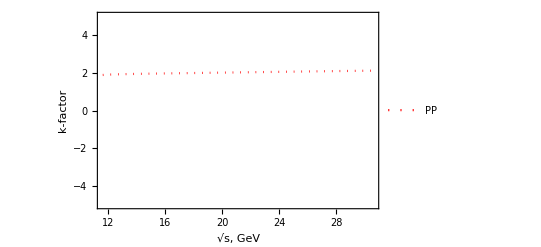

```mathematica
KFactorPlot=ListPlot[
{KFactors["PP"]⟦3;;⟧,KFactors["PV"]⟦3;;⟧,KFactors["VV"]⟦3;;⟧}[[2]],
Joined->True,
PlotRange->{Automatic,{-5,5}},
Frame->True,FrameLabel->{{"k-factor",""},{"√s, GeV",""}},
PlotStyle->{Directive[Dotted,Red],Directive[Dashed,Blue],Directive[DotDashed,Black]},
PlotLegends->{"PP","PV","VV"}
]
```

```mathematica
Export["costheta.pdf",CosThetaPlots[[2]]]
Export["full.pdf",FullCrossSectionPlots[[2]]]
Export["kFactor.pdf",KFactorPlot]
```

costheta.pdf

full.pdf

kFactor.pdf